# Omicron US analysis: Plotting partitioned case counts and Rt

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/omicron-us

```mathematica
dataset="omicron-us";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=250;
```

```mathematica
statesToDrop={"California","Colorado","North Carolina"};
```

```mathematica
gridCount=4;
```

## Setup

### Variants

```mathematica
variants={"other","Delta","Omicron"};
```

```mathematica
n=Length[variants]
```

3

```mathematica
legendPanel=PointLegend[colors,variants,LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}]
```

PointLegend[colors,{other,Delta,Omicron},LegendMarkerSize→20,LegendLayout→{Row,1},Spacings→{0,1}]

### Colors

```mathematica
colors=Prepend[Table[ColorData["Rainbow"][i],{i,{0.3,0.95}}],Gray]
```

{GrayLevel[0.5],RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.8739574, 0.2607876000000001, 0.15481040000000004]}

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-10-15","2021-11-01","2021-11-15","2021-12-01","2021-12-15","2022-01-01"};
```

### Smoothing functions

```mathematica
smoothed[dateSeries_]:=Map[{#[[4,1]],N[Mean[#[[All,2]]]]}&,Partition[dateSeries,7,1]]
```

```mathematica
simplePrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[1]],N[(#1[[2]])/(0.0001+#2[[2]])]}&,{dateSeriesPositives,dateSeriesTotals}]
```

```mathematica
smoothedPrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[4,1]],N[Total[#1[[All,2]]]/(0.0001+Total[#2[[All,2]]])]}&,{Partition[dateSeriesPositives,7,1],Partition[dateSeriesTotals,7,1]}]
```

```mathematica
gappedPartition[list_,n_]:=Partition[list,n,n,1,""]
```

## Rt estimates

Using GARW (growth autoregressive random walk) model

```mathematica
rtData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_Rt-combined-"<>model<>".tsv"];
```

```mathematica
header=rtData[[1]]
```

{date,location,variant,median_R,median_freq,R_upper_95,R_lower_95,R_upper_80,R_lower_80,R_upper_50,R_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_R→4,median_freq→5,R_upper_95→6,R_lower_95→7,R_upper_80→8,R_lower_80→9,R_upper_50→10,R_lower_50→11}

```mathematica
rtData=Drop[rtData,1];
```

```mathematica
startDate=First[Sort[rtData[[All,1]]]]
```

2021-10-15

```mathematica
modelEndDate=Last[Sort[rtData[[All,1]]]]
```

2022-01-11

```mathematica
endDate=Last[Sort[rtData[[All,1]]]]
```

2022-01-11

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
states=Union[rtData[[All,2]]]
```

{Arizona,California,Colorado,Connecticut,Florida,Georgia,Illinois,Indiana,Kentucky,Louisiana,Maryland,Massachusetts,Michigan,Minnesota,Nebraska,Nevada,New Jersey,New Mexico,New York,North Carolina,North Dakota,Ohio,Oregon,Pennsylvania,Tennessee,Texas,Utah,Vermont,Virginia,Washington,Wisconsin}

```mathematica
states=DeleteCases[states,x_/;MemberQ[statesToDrop,x]]
```

{Arizona,Connecticut,Florida,Georgia,Illinois,Indiana,Kentucky,Louisiana,Maryland,Massachusetts,Michigan,Minnesota,Nebraska,Nevada,New Jersey,New Mexico,New York,North Dakota,Ohio,Oregon,Pennsylvania,Tennessee,Texas,Utah,Vermont,Virginia,Washington,Wisconsin}

```mathematica
Length[states]
```

28

Only keep Rt data points when the variant is frequent enough to have a good estimate

```mathematica
rtData=Cases[rtData,x_/;x[[5]]>0.001];
```

```mathematica
rtData=DeleteCases[rtData,x_/;x[[2]]=="South Africa"&&x[[5]]<0.01];
```

```mathematica
rtGather[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
rtGatherLower[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,9}]]
```

```mathematica
rtGatherUpper[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
variantCountryRtPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=rtGather[country,variant];
lowerSeries=rtGatherLower[country,variant];
upperSeries=rtGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{35,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,7}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,0}],Dashed,Black,Line[{{startDate,1},{modelEndDate,1}}]}]
]
```

```mathematica
variantsCountryRtLabelPlot[country_,variants_]:=Module[{medians,finalDates,finalValues},
medians=Map[Last[rtGather[country,#]]&,variants];
finalDates=medians[[All,1]];
finalValues=medians[[All,2]];
DateListPlot[{},Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{30,5},{15,10}},PlotRange->{{startDate,DatePlus[modelEndDate,10]},
{0,7}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Prolog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],MapThread[Text[Style[NumberForm[Round[#2,0.1],{2,1}],Black,FontSize->10,FontFamily->"Helvetica"],{DatePlus[#1,1],#2},{-1,0}]&,{finalDates,finalValues}],Dashed,Black,Line[{{startDate,1},{modelEndDate,1}}]}]
]
```

```mathematica
countryRtPlot[country_]:=Show[variantsCountryRtLabelPlot[country,variants[[2;;3]]],Table[variantCountryRtPlot[country,variants[[i]],colors[[i]]],{i,2,3}]]
```

```mathematica
panels=Map[countryRtPlot,states];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

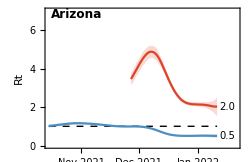
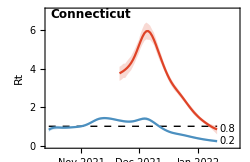
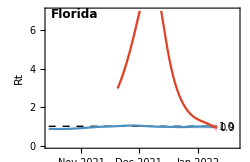
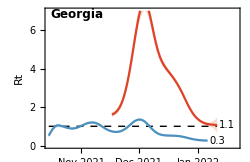
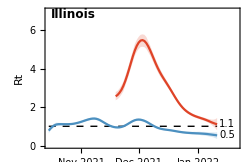
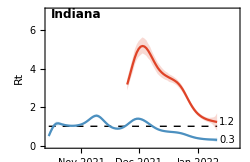
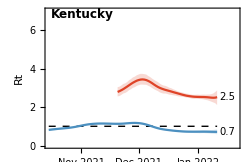
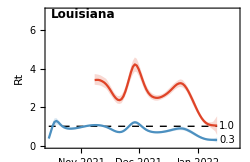
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-rt.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_variant-rt.png

Rt

```mathematica
Map[#->{rtGather[#,"Omicron"][[-1,1]],Round[rtGather[#,"Omicron"][[-1,2]],0.1],Round[rtGatherLower[#,"Omicron"][[-1,2]],0.1],Round[rtGatherUpper[#,"Omicron"][[-1,2]],0.1]}&,states]
```

{Arizona→{2022-01-11,2.,1.5,2.5},Connecticut→{2022-01-11,0.8,0.6,1.1},Florida→{2022-01-11,0.9,0.6,1.2},Georgia→{2022-01-11,1.1,0.6,1.5},Illinois→{2022-01-11,1.1,0.8,1.4},Indiana→{2022-01-11,1.2,0.8,1.7},Kentucky→{2022-01-11,2.5,2.1,2.9},Louisiana→{2022-01-11,1.,0.5,1.5},Maryland→{2022-01-11,0.8,0.6,1.},Massachusetts→{2022-01-11,1.2,0.8,1.4},Michigan→{2022-01-11,0.9,0.5,1.3},Minnesota→{2022-01-11,2.1,1.5,2.6},Nebraska→{2022-01-11,1.2,0.9,1.6},Nevada→{2022-01-11,1.5,1.1,1.9},New Jersey→{2022-01-11,0.8,0.6,1.},New Mexico→{2022-01-11,1.7,1.1,2.2},New York→{2022-01-11,0.9,0.7,1.1},North Dakota→{2022-01-11,2.3,2.2,2.5},Ohio→{2022-01-11,1.,0.7,1.2},Oregon→{2022-01-11,1.3,0.9,1.8},Pennsylvania→{2022-01-11,1.2,0.9,1.4},Tennessee→{2022-01-11,1.1,0.7,1.4},Texas→{2022-01-11,0.7,0.3,1.2},Utah→{2022-01-11,1.8,1.5,2.2},Vermont→{2022-01-07,2.,1.6,2.3},Virginia→{2022-01-11,1.1,0.8,1.4},Washington→{2022-01-11,1.5,1.,2.},Wisconsin→{2022-01-11,1.5,1.1,1.9}}

## Little r estimates

Using fixed growth model

```mathematica
rData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_little-r-combined-"<>model<>".tsv"];
```

```mathematica
header=rData[[1]]
```

{date,location,variant,median_r,median_freq,r_upper_95,r_lower_95,r_upper_80,r_lower_80,r_upper_50,r_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_r→4,median_freq→5,r_upper_95→6,r_lower_95→7,r_upper_80→8,r_lower_80→9,r_upper_50→10,r_lower_50→11}

```mathematica
rData=Drop[rData,1];
```

Only keep Rt data points when the variant is frequent enough to have a good estimate

```mathematica
rData=Cases[rData,x_/;x[[5]]>0.001];
```

```mathematica
rGather[country_,variant_]:=Cases[rData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
rGatherLower[country_,variant_]:=Cases[rData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,9}]]
```

```mathematica
rGatherUpper[country_,variant_]:=Cases[rData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
variantCountryLittleRPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=rGather[country,variant];
lowerSeries=rGatherLower[country,variant];
upperSeries=rGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{45,5},{15,10}},Joined->True,PlotRange->{{startDate,DatePlus[modelEndDate,7]},
{-0.35,0.5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,0}],Dashed,Black,Line[{{startDate,0},{modelEndDate,0}}]}]
]
```

```mathematica
variantsCountryLittleRLabelPlot[country_,variants_]:=Module[{medians,finalDates,finalValues},
medians=Map[Last[rGather[country,#]]&,variants];
finalDates=medians[[All,1]];
finalValues=medians[[All,2]];
DateListPlot[{},Frame->{True,True,False,False},FrameLabel->{"","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{42,5},{15,10}},PlotRange->{{startDate,DatePlus[modelEndDate,15]},
{-0.35,0.5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Prolog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],MapThread[Text[Style[NumberForm[Round[#2,0.01],{2,2}],Black,FontSize->10,FontFamily->"Helvetica"],{DatePlus[#1,1],#2},{-1,0}]&,{finalDates,finalValues}],Dashed,Black,Line[{{startDate,0},{modelEndDate,0}}]}]
]
```

```mathematica
countryLittleRPlot[country_]:=Show[variantsCountryLittleRLabelPlot[country,variants[[2;;3]]],Table[variantCountryLittleRPlot[country,variants[[i]],colors[[i]]],{i,2,3}]]
```

```mathematica
panels=Map[countryLittleRPlot,states];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

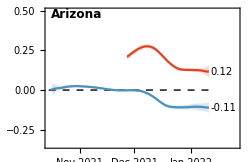
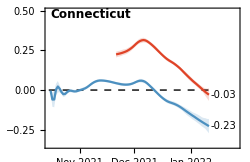
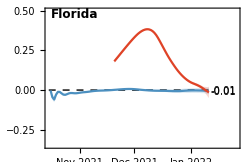
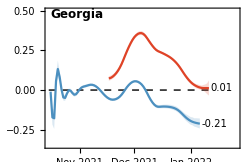
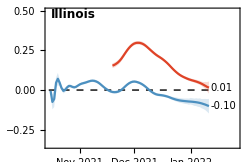
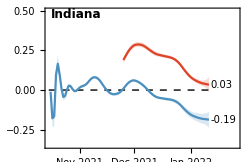
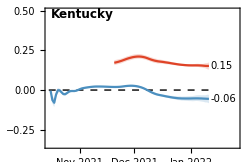
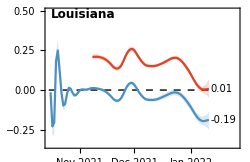
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-little-r.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_variant-little-r.png

Little r

```mathematica
Map[#->{rGather[#,"Omicron"][[-1,1]],Round[rGather[#,"Omicron"][[-1,2]],0.01],Round[rGatherLower[#,"Omicron"][[-1,2]],0.01],Round[rGatherUpper[#,"Omicron"][[-1,2]],0.01]}&,states]
```

{Arizona→{2022-01-11,0.12,0.08,0.15},Connecticut→{2022-01-11,-0.03,-0.07,0.01},Florida→{2022-01-11,-0.01,-0.05,0.02},Georgia→{2022-01-11,0.01,-0.03,0.06},Illinois→{2022-01-11,0.01,-0.02,0.05},Indiana→{2022-01-11,0.03,-0.01,0.08},Kentucky→{2022-01-11,0.15,0.13,0.17},Louisiana→{2022-01-11,0.01,-0.05,0.07},Maryland→{2022-01-11,-0.03,-0.06,0.},Massachusetts→{2022-01-11,0.02,-0.01,0.06},Michigan→{2022-01-11,-0.01,-0.07,0.04},Minnesota→{2022-01-11,0.13,0.09,0.17},Nebraska→{2022-01-11,0.03,0.,0.07},Nevada→{2022-01-11,0.07,0.03,0.1},New Jersey→{2022-01-11,-0.03,-0.06,-0.01},New Mexico→{2022-01-11,0.08,0.03,0.12},New York→{2022-01-11,-0.02,-0.05,0.02},North Dakota→{2022-01-11,0.14,0.13,0.15},Ohio→{2022-01-11,0.,-0.04,0.03},Oregon→{2022-01-11,0.04,0.,0.09},Pennsylvania→{2022-01-11,0.02,0.,0.05},Tennessee→{2022-01-11,0.01,-0.02,0.05},Texas→{2022-01-11,-0.05,-0.13,0.03},Utah→{2022-01-11,0.1,0.07,0.13},Vermont→{2022-01-07,0.11,0.08,0.14},Virginia→{2022-01-11,0.02,-0.01,0.06},Washington→{2022-01-11,0.07,0.03,0.11},Wisconsin→{2022-01-11,0.07,0.03,0.1}}

Doubling time

```mathematica
Map[#->{rGather[#,"Omicron"][[-1,1]],Round[Log[2]/rGather[#,"Omicron"][[-1,2]],0.1],Round[Log[2]/rGatherUpper[#,"Omicron"][[-1,2]],0.1],Round[Log[2]/rGatherLower[#,"Omicron"][[-1,2]],0.1]}&,states]
```

{Arizona→{2022-01-11,6.,4.6,8.9},Connecticut→{2022-01-11,-23.6,59.7,-10.1},Florida→{2022-01-11,-47.8,33.2,-13.7},Georgia→{2022-01-11,60.7,11.4,-19.9},Illinois→{2022-01-11,46.3,12.8,-30.1},Indiana→{2022-01-11,20.7,8.5,-71.3},Kentucky→{2022-01-11,4.5,4.,5.4},Louisiana→{2022-01-11,96.7,10.1,-14.4},Maryland→{2022-01-11,-22.1,643.8,-11.4},Massachusetts→{2022-01-11,32.,12.1,-53.5},Michigan→{2022-01-11,-58.5,18.7,-10.3},Minnesota→{2022-01-11,5.5,4.1,8.},Nebraska→{2022-01-11,20.4,9.8,-149.9},Nevada→{2022-01-11,10.3,6.6,21.1},New Jersey→{2022-01-11,-22.,-95.1,-11.4},New Mexico→{2022-01-11,8.5,5.6,20.},New York→{2022-01-11,-42.9,38.2,-13.7},North Dakota→{2022-01-11,4.8,4.5,5.2},Ohio→{2022-01-11,-154.9,23.2,-19.4},Oregon→{2022-01-11,17.1,8.1,-169.1},Pennsylvania→{2022-01-11,30.1,12.8,-243.5},Tennessee→{2022-01-11,52.9,13.4,-29.2},Texas→{2022-01-11,-14.1,27.5,-5.5},Utah→{2022-01-11,7.,5.3,9.5},Vermont→{2022-01-07,6.1,5.1,8.2},Virginia→{2022-01-11,31.5,11.6,-63.4},Washington→{2022-01-11,9.9,6.2,25.4},Wisconsin→{2022-01-11,9.8,6.6,21.1}}

## Prevalence

Using fixed growth model

```mathematica
pData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_I-combined-"<>model<>".tsv"];
```

```mathematica
header=pData[[1]]
```

{date,location,variant,median_I,I_upper_95,I_lower_95,I_upper_80,I_lower_80,I_upper_50,I_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_I→4,I_upper_95→5,I_lower_95→6,I_upper_80→7,I_lower_80→8,I_upper_50→9,I_lower_50→10}

```mathematica
pData=Drop[pData,1];
```

Only keep data points with incidence

```mathematica
pData=Cases[pData,x_/;x[[4]]>0.9];
```

```mathematica
pGather[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
pGatherLower[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
pGatherUpper[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListLogPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{20,240000}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,0},{modelEndDate,0}}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,2,3}]]
```

```mathematica
panels=Map[countryPrevalencePlot,states];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

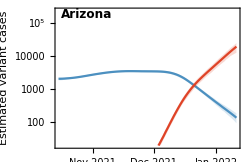
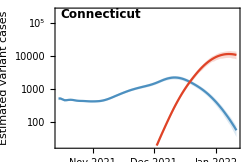
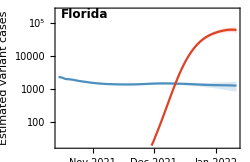
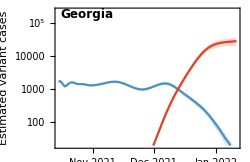
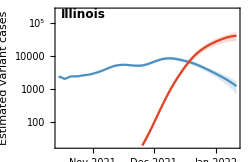
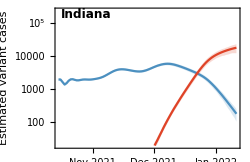
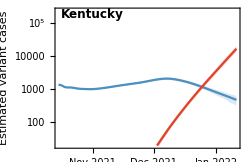
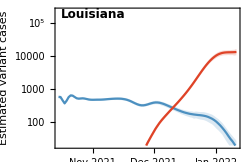
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_variant-estimated-log-cases.png

```mathematica
yMaxForCountry[country_]:=Max[Flatten[Table[pGatherUpper[country,variant][[All,2]],{variant,variants}]]]
```

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,yMaxForCountry[country]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,0},{modelEndDate,0}}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,2,3}]]
```

```mathematica
panels=Map[countryPrevalencePlot,states];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

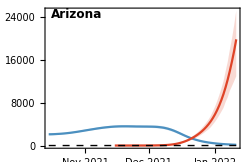
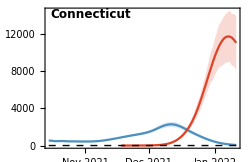
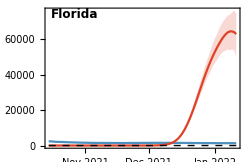
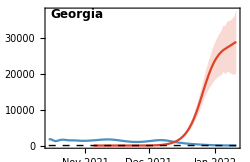
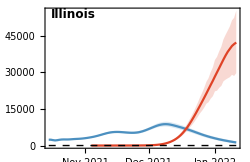
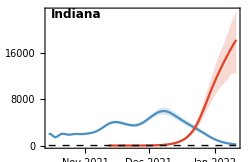
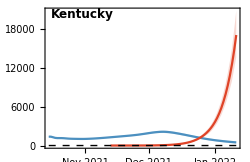
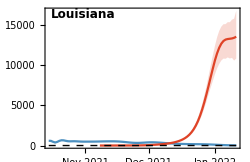
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_variant-estimated-cases.png

Prevalence

```mathematica
Map[#->{pGather[#,"Omicron"][[-1,1]],Round[pGather[#,"Omicron"][[-1,2]]],Round[pGatherLower[#,"Omicron"][[-1,2]]],Round[pGatherUpper[#,"Omicron"][[-1,2]]]}&,states]
```

{Arizona→{2022-01-11,19766,12880,25079},Connecticut→{2022-01-11,11092,8148,13957},Florida→{2022-01-11,62876,50329,74447},Georgia→{2022-01-11,29021,20103,37710},Illinois→{2022-01-11,42157,29605,55145},Indiana→{2022-01-11,18295,12447,23331},Kentucky→{2022-01-11,17038,13570,20774},Louisiana→{2022-01-11,13577,10853,16815},Maryland→{2022-01-11,10934,8735,12997},Massachusetts→{2022-01-11,33858,22840,43011},Michigan→{2022-01-11,18595,10818,24479},Minnesota→{2022-01-11,12253,9367,14754},Nebraska→{2022-01-11,3590,2740,4433},Nevada→{2022-01-11,6383,4379,8025},New Jersey→{2022-01-11,33818,27250,39957},New Mexico→{2022-01-11,4663,2521,6677},New York→{2022-01-11,64578,44304,83046},North Dakota→{2022-01-11,2356,1810,2825},Ohio→{2022-01-11,19130,13313,25399},Oregon→{2022-01-11,14502,7686,19989},Pennsylvania→{2022-01-11,33746,23344,44150},Tennessee→{2022-01-11,14999,12317,17707},Texas→{2022-01-11,45573,33493,56380},Utah→{2022-01-11,14273,10291,18292},Vermont→{2022-01-07,1517,1208,1794},Virginia→{2022-01-11,37021,25822,46758},Washington→{2022-01-11,21535,16630,26230},Wisconsin→{2022-01-11,19708,14712,24060}}

## Frequency

```mathematica
fData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_freq-combined-"<>model<>".tsv"];
```

```mathematica
header=fData[[1]]
```

{date,location,variant,median_freq,freq_upper_95,freq_lower_95,freq_upper_80,freq_lower_80,freq_upper_50,freq_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_freq→4,freq_upper_95→5,freq_lower_95→6,freq_upper_80→7,freq_lower_80→8,freq_upper_50→9,freq_lower_50→10}

```mathematica
fData=Drop[fData,1];
```

```mathematica
fGather[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
fGatherLower[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
fGatherUpper[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryFrequencyPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=fGather[country,variant];
lowerSeries=fGatherLower[country,variant];
upperSeries=fGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated Omicron frequency"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,1}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Table[{i,ToString[Round[100*i]]<>"%"},{i,0,1,0.2}],Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,0},{endDate,0}}]}]
]
```

```mathematica
countryFrequencyPlot[country_]:=variantCountryFrequencyPlot[country,variants[[3]],colors[[3]]]
```

```mathematica
panels=Map[countryFrequencyPlot,states];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

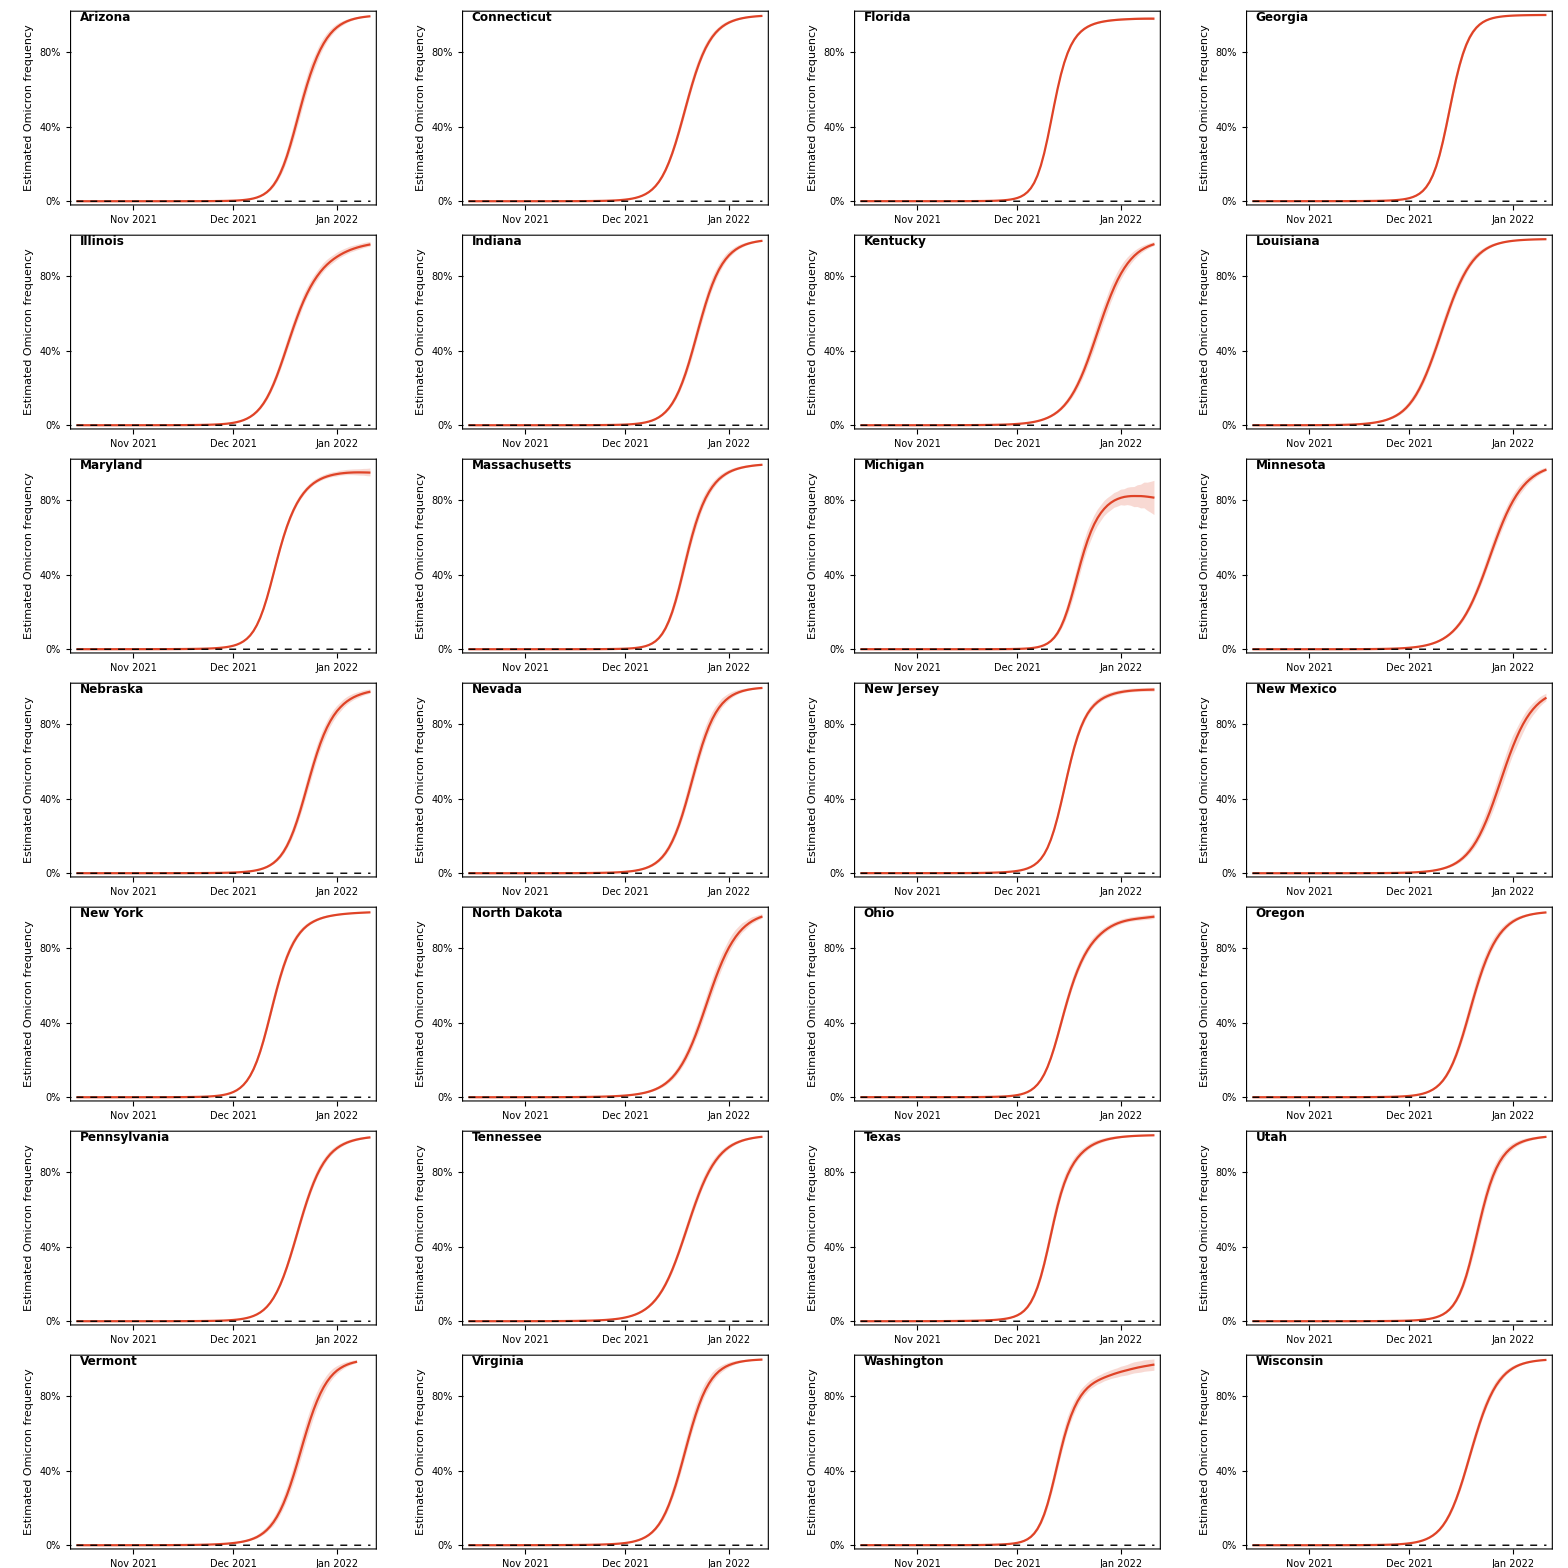

```mathematica
fig=Grid[gappedPartition[panels,gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-frequency.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_variant-estimated-frequency.png

Frequency

```mathematica
Map[#->{fGather[#,"Omicron"][[-1,1]],Round[fGather[#,"Omicron"][[-1,2]],0.01],Round[fGatherLower[#,"Omicron"][[-1,2]],0.01],Round[fGatherUpper[#,"Omicron"][[-1,2]],0.01]}&,states]
```

{Arizona→{2022-01-11,0.99,0.99,1.},Connecticut→{2022-01-11,0.99,0.99,1.},Florida→{2022-01-11,0.98,0.97,0.99},Georgia→{2022-01-11,1.,1.,1.},Illinois→{2022-01-11,0.97,0.96,0.98},Indiana→{2022-01-11,0.99,0.99,0.99},Kentucky→{2022-01-11,0.97,0.96,0.98},Louisiana→{2022-01-11,1.,1.,1.},Maryland→{2022-01-11,0.95,0.93,0.97},Massachusetts→{2022-01-11,0.99,0.99,0.99},Michigan→{2022-01-11,0.81,0.72,0.9},Minnesota→{2022-01-11,0.96,0.95,0.97},Nebraska→{2022-01-11,0.97,0.96,0.99},Nevada→{2022-01-11,0.99,0.99,1.},New Jersey→{2022-01-11,0.99,0.97,1.},New Mexico→{2022-01-11,0.94,0.92,0.96},New York→{2022-01-11,0.99,0.99,1.},North Dakota→{2022-01-11,0.97,0.96,0.98},Ohio→{2022-01-11,0.97,0.96,0.98},Oregon→{2022-01-11,0.99,0.99,1.},Pennsylvania→{2022-01-11,0.99,0.98,0.99},Tennessee→{2022-01-11,0.99,0.99,0.99},Texas→{2022-01-11,1.,1.,1.},Utah→{2022-01-11,0.99,0.98,1.},Vermont→{2022-01-07,0.99,0.98,0.99},Virginia→{2022-01-11,1.,0.99,1.},Washington→{2022-01-11,0.97,0.94,1.},Wisconsin→{2022-01-11,0.99,0.99,1.}}

## Phase diagrams

Convert to cases per 100k per day

```mathematica
perCapitaPGather[state_,variant_]:=Module[{popSize,stateName},
stateName=StringReplace[state," "->""];
popSize=QuantityMagnitude[AdministrativeDivisionData[{stateName, "UnitedStates"},"Population"]];
Map[{#[[1]],100000*#[[2]]/popSize}&,pGather[state,variant]]
]
```

```mathematica
compareWithDate[dateSeries1_, dateSeries2_] := Map[{#[[1, 1]], #[[1, 2]], #[[2, 2]]} &, DeleteCases[Map[{FirstCase[dateSeries1, x_ /; x[[1]] == #], FirstCase[dateSeries2, x_ /; x[[1]] == #]} &, dates], {x_, y_} /; x == Missing["NotFound"] || y == Missing["NotFound"]]]
```

```mathematica
phaseGather[country_,variant_]:=compareWithDate[perCapitaPGather[country,variant],rGather[country,variant]][[All,{2,3}]]
```

```mathematica
countryRPrevalencePhasePlot[country_]:=Module[{pairsOmicron},
pairsOmicron=phaseGather[country,"Omicron"];
ListLogLinearPlot[{pairsOmicron,{Last[pairsOmicron]}},Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->True,PlotRange->{{2,500},
{-0.25,0.45}},Joined->{True,False},PlotMarkers->{None,{"•",Scaled[0.12]}},PlotStyle->{colors[[3]],colors[[3]]},
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
]
```

```mathematica
panels=Map[countryRPrevalencePhasePlot,states];
```

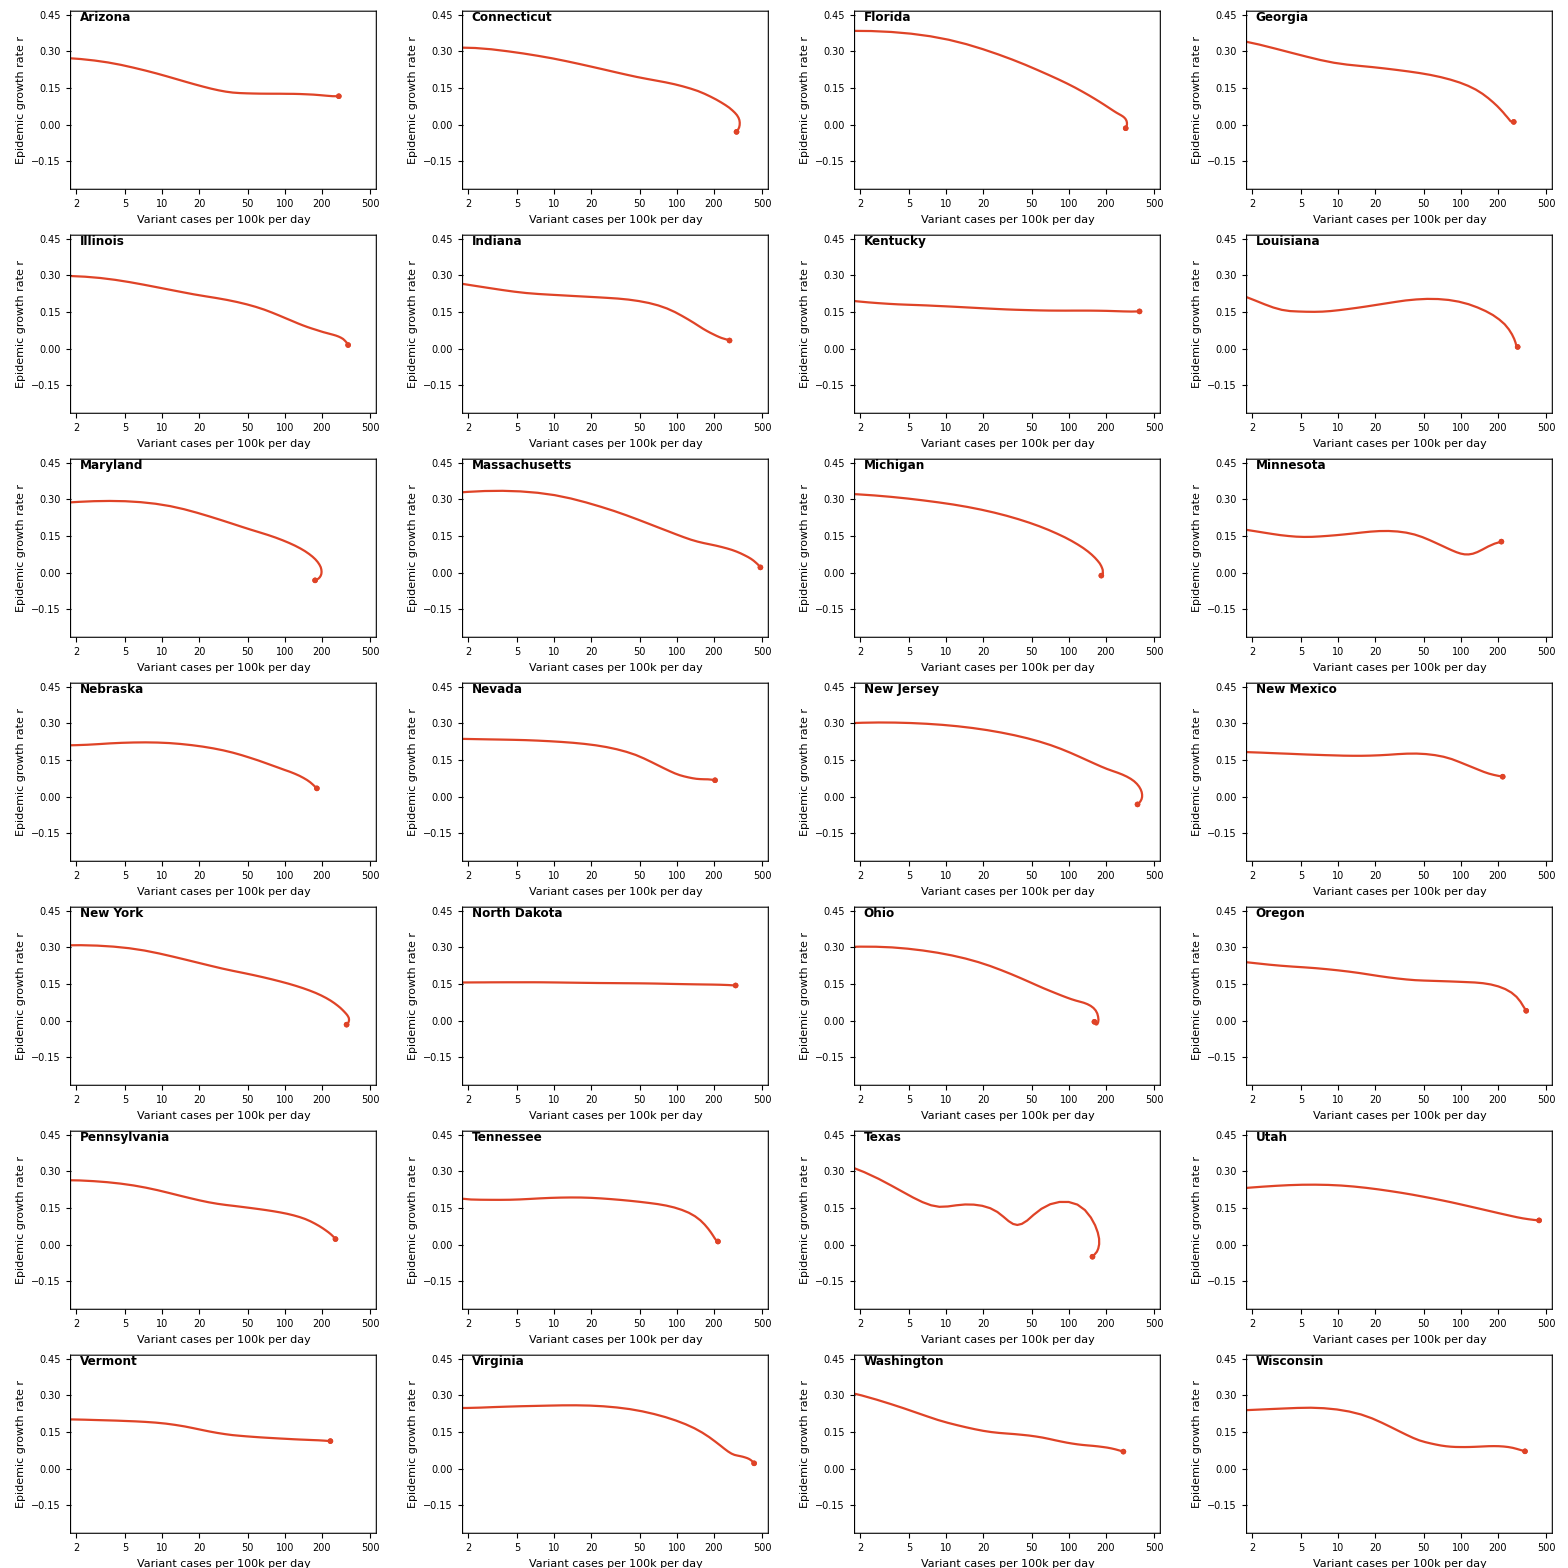

```mathematica
fig=Grid[gappedPartition[panels,gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-cases-vs-rt.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_variant-cases-vs-rt.png

```mathematica
stateLines=Map[With[{pairs=phaseGather[#,"Omicron"]},pairs]&,states];
```

```mathematica
figLines=ListLogLinearPlot[stateLines,Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->True,PlotRange->{{2,500},
{-0.15,0.4}},PlotStyle->Directive[colors[[3]],Opacity[0.5]]];
```

```mathematica
statePoints=Map[With[{pairs=phaseGather[#,"Omicron"]},Last[pairs]]&,states];
```

```mathematica
figPoints=ListLogLinearPlot[statePoints,Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->False,PlotRange->{{2,150},
{-0.15,0.4}},PlotStyle->Directive[colors[[3]]],PlotMarkers->{"•",Scaled[0.1]}];
```

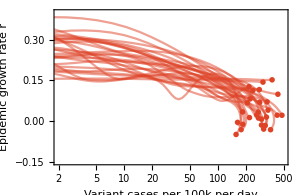

```mathematica
fig=Show[figLines,figPoints]
```

```mathematica
Export["figures/"<>dataset<>"_variant-cases-vs-rt-overlay.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_variant-cases-vs-rt-overlay.png